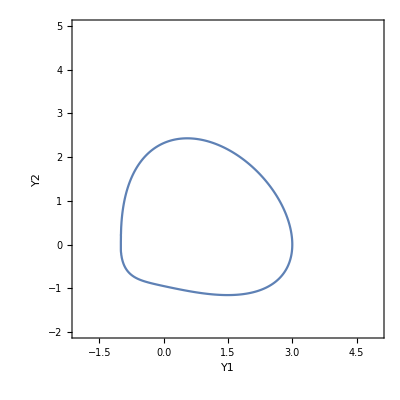

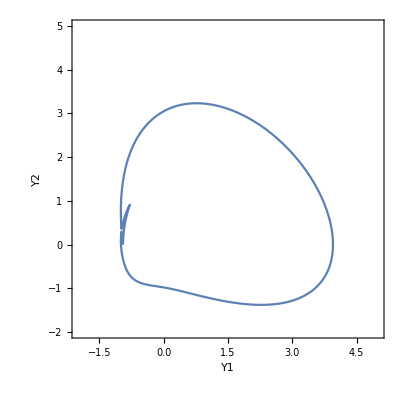

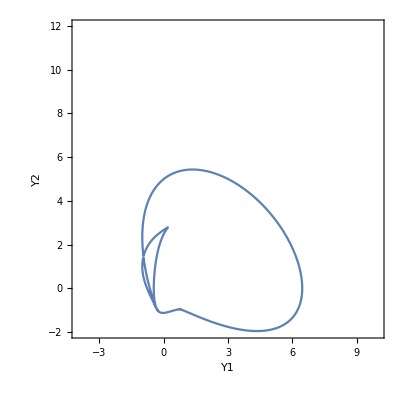

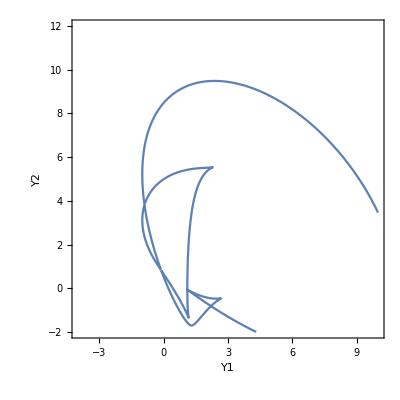

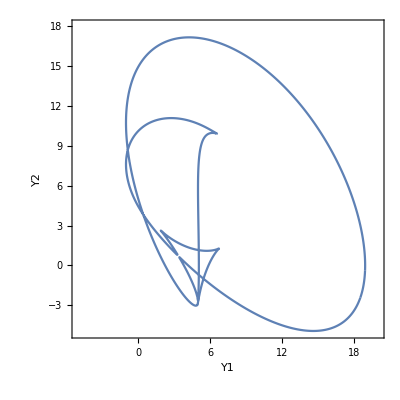

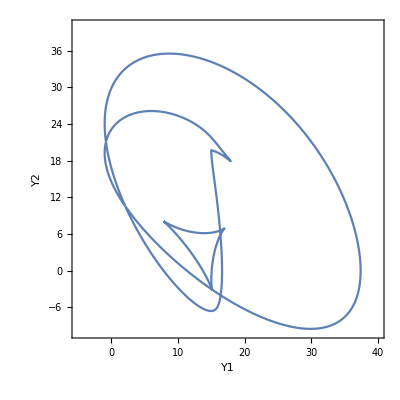

```mathematica
Quit[]

A1 = {{1, 1, 1},{1,  2,0}, {1, 0, 2}};
A2 = {{3, -1, 0},{-1,  0,-1}, {0, -1, 1}};
A3 = IdentityMatrix[3];
b1 = {1,1,1};
b2 = {1,0,-1};
b3 = {0,0,0};



y1 =x1^2+(2*x2+2*x3+2)*x1+2*x2^2+2*x2+2*x3^2+2*x3;
y2 = 2*x1-2*x3-2*x1*x2-2*x2*x3+3*x1^2+x3^2;
y3 = x1^2 + x2^2 + x3^2;

(* the proper way to define quadratic form
{x1, x2, x3}.A1.{x1,x2,x3}+b1.{x1,x2,x3} *)


 S = Solve[y1==Y1 && y2 ==Y2 && y3 == Y3 , {x1, x2, x3}] 


(* for Y3 = 1? *)
(*
Qu = 48 Y1^2-32 Y1^3+5 Y1^4-192 Y2-64 Y1 Y2+32 Y1^2 Y2+64 Y2^2+(768+256 Y1-112 Y1^2-8 Y1^3-1152 Y2-128 Y1 Y2+64 Y1^2 Y2+256 Y2^2)z+(4160+608 Y1-472 Y1^2+44 Y1^3-2944 Y2+64 Y1 Y2+32 Y1^2 Y2+384 Y2^2) z^2+(9408-256 Y1-248 Y1^2-3968 Y2+256 Y1 Y2+256 Y2^2) z^3+(11200-1456 Y1+94 Y1^2-2848 Y2+128 Y1 Y2+64 Y2^2) z^4+(7216-824 Y1-960 Y2) z^5+(2472+44 Y1-96 Y2) z^6+696 z^7+261 z^8;
*)
Qu = 32 Y1^2+8 Y1^3+5 Y1^4+64 Y1 Y2+32 Y1^2 Y2+64 Y2^2-128 Y3-160 Y1 Y3-104 Y1^2 Y3-40 Y1^3 Y3-320 Y2 Y3-128 Y1 Y2 Y3+336 Y3^2+320 Y1 Y3^2+120 Y1^2 Y3^2+128 Y2 Y3^2-288 Y3^3-160 Y1 Y3^3+80 Y3^4+(-256 Y1-48 Y1^2-8 Y1^3-384 Y2+128 Y1 Y2+64 Y1^2 Y2+256 Y2^2+704 Y3+160 Y1 Y3-64 Y1^2 Y3-1024 Y2 Y3-256 Y1 Y2 Y3+448 Y3^2+352 Y1 Y3^2+256 Y2 Y3^2-384 Y3^3) z+(768-512 Y1-152 Y1^2+44 Y1^3-1536 Y2+192 Y1 Y2+32 Y1^2 Y2+384 Y2^2+3232 Y3+368 Y1 Y3-320 Y1^2 Y3-1536 Y2 Y3-128 Y1 Y2 Y3+736 Y3^2+752 Y1 Y3^2+128 Y2 Y3^2-576 Y3^3) z^2+(2688-736 Y1-248 Y1^2-2688 Y2+256 Y1 Y2+256 Y2^2+6112 Y3+480 Y1 Y3-1280 Y2 Y3+608 Y3^2) z^3+(4512-808 Y1+94 Y1^2-2400 Y2+128 Y1 Y2+64 Y2^2+5624 Y3-648 Y1 Y3-448 Y2 Y3+1064 Y3^2) z^4+(4368-824 Y1-960 Y2+2848 Y3) z^5+(2616+44 Y1-96 Y2-144 Y3) z^6+696 z^7+261 z^8;
Quq = Discriminant[Qu,z];

ContourPlot3D[Quq==0,{Y1,-5,35},{Y2,-10,40},{Y3,0,9}, Axes->True,AxesStyle->Directive[Black,30],MaxRecursion->4]



(*

Qplot = Quq/.{Y3 -> 1/3};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-2,5},{Y2,-2,5},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
Qplot = Quq/.{Y3 -> 1/2};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-2,5},{Y2,-2,5},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
Qplot = Quq/.{Y3 -> 1};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-4,10},{Y2,-2,12},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
Qplot = Quq/.{Y3 -> 2};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-4,10},{Y2,-2,12},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
Qplot = Quq/.{Y3 -> 4};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-5,20},{Y2,-5,18},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
Qplot = Quq/.{Y3 -> 9};
poly2 = Factor[Qplot][[4]];
ContourPlot[poly2==0,{Y1,-5,40},{Y2,-10,40},Axes->True,Frame->True,ContourShading->Automatic,AxesStyle->Directive[Black,30],AxesLabel->{Style["Y1",FontSize->22],Style["Y2",FontSize->22]}, MaxRecursion->4]
*)
```